# Mínimos cuadrados

La siguiente función calcula la recta de mínimos cuadrados ordinarios de un conjunto de datos, muestra la gráfica con la recta y los intervalos de confianza para E (Y) y Y, además realiza y muestra diversos cálculos de importancia .
  
  Argumentos :
 datos : Lista de los puntos sobres lo cuales se hará la regresión,
inter : intervalo en x donde se quiere que se muestre la gráfica
alpha : valor de α para generar los intervalos de confianza

Nota: La teoría y notación detrás de estos cálculos provine del libro “Estadistica Matematica con Aplicaciones” de los autores Wackerly, Mendenhall

```mathematica
MinimosInter[datos_,inter_,alpha_]:=Module[{},
n=Length[datos];
x=datos[[All,1]]; (*Separamos de la lista los correspondientes a la variable x y y *)
y=datos[[All,2]];
mx=Mean@x;my=Mean@y; (*Calculamos la media*)
vx=Variance@x;vy=Variance@y; (*Calculamos la varianza*)
Subscript[S, xy]=∑_(i=1)^n (x[[i]]-mx)(y[[i]]-my); (*Se calculan los valores para obtener la recta de MCO*);
Subscript[S, xx]=∑_(i=1)^n (x[[i]]-mx)^2; Subscript[S, yy]=∑_(i=1)^n (y[[i]]-my)^2;
Subscript[β, 1]=Subscript[S, xy]/Subscript[S, xx]; Subscript[β, 0]=my-Subscript[β, 1]*mx;
(* recta de minimos cuadrados *);
mini[k_]:=Subscript[β, 0]+Subscript[β, 1] *k; (*Creamos una función de la recta de MCO*)

SSE=Subscript[S, yy]-Subscript[β, 1] Subscript[S, xy];
s2=SSE/(n-2); s=√s2;
Subscript[c, 00]=∑_(i=1)^n x[[i]]^2/(n Subscript[S, xx]);vb0=Subscript[c, 00] s2;
Subscript[c, 11]=1/Subscript[S, xx];vb1=Subscript[c, 11] s2;
Subscript[c, 01]=-mx/Subscript[S, xx];cov= Subscript[c, 01] s^2;
r=Subscript[S, xy]/(√(Subscript[S, xx] Subscript[S, yy]));r2=r^2;

ta2=Quantile[StudentTDistribution[n-2],1-alpha/2] (*Calculamos el quantil α/2 de la distribución T *);
EyInf[k_]:=mini[k]-ta2* s √(1/n+(k-mx)^2/Subscript[S, xx])(*Creamos las funciones de los limites de los intervalos para poder graficarlas*);
EySup[k_]:=mini[k]+ta2* s √(1/n+(k-mx)^2/Subscript[S, xx]);
YInf[k_]:=mini[k]-ta2* s √(1+1/n+(k-mx)^2/Subscript[S, xx]);
YSup[k_]:=mini[k]+ta2* s √(1+1/n+(k-mx)^2/Subscript[S, xx]);
(*Creamos los prints donde se mostrarán todos los resultados*);
Print["Tenemos \n x̄=",N@mx,"\n ȳ=",N@my,"\n S_xy=",N@Subscript[S, xy],"\n S_xx=",N@Subscript[S, xx],"\n V(x)=",N@vx,"\n V(y)=",N@vy];
Print["Y así \n (β̂)_1=",N@Subscript[β, 1],"\n (β̂)_0=",N@Subscript[β, 0],"\n Por lo tanto de recta de MCO es \n",Style["ŷ=",Blue],Style[N[Subscript[β, 0] "x"+Subscript[β, 1]],Blue]];
Print["\n Además \n SSE=",N@SSE,"\n s^2=",N@s2,"\n s=",N@s];
Print["\n V((β̂)_0)=",N@vb0,"\n V((β̂)_1)=",N@vb1,"\n cov((β̂)_0,(β̂)_1)=",N@cov];
Print["\n r=",N@r,"\n r^2=",N@r2];
(*Mostramos la gráfica de la recta MCO y los intervalos de confianza *);
Show[ListPlot[datos],Plot[{mini[k],EyInf[k],EySup[k],YInf[k],YSup[k]},{k,inter[[1]]-1,inter[[2]]+1},PlotStyle->{Blue,Directive[Dashed,Orange],Directive[Dashed,Orange],Directive[Dashed,Green],Directive[Dashed,Green]},PlotLegends->{"Recta de MCO",None,"Intervalo de confianza para E(Y)",None,"Intervalo de confianza para Y"}],PlotRange->All]

]
```

#### Ejemplo

Tenemos 
 x̄=0.
 ȳ=1.
 S_xy=7.
 S_xx=10.
 V(x)=2.5
 V(y)=1.5

Y así 
 (β̂)_1=0.7
 (β̂)_0=1.
 Por lo tanto de recta de MCO es 
ŷ=0.7+x

Además 
 SSE=1.1
 s^2=0.366667
 s=0.60553

V((β̂)_0)=0.0733333
 V((β̂)_1)=0.0366667
 cov((β̂)_0,(β̂)_1)=0.

r=0.903696
 r^2=0.816667

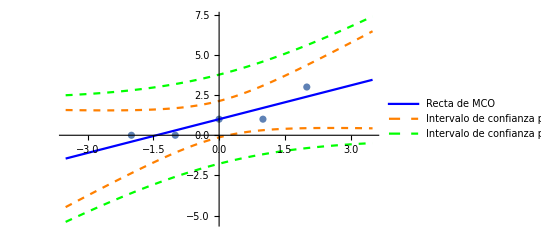

```mathematica
d={{-2,0},{-1,0},{0,1},{1,1},{2,3}};
MinimosInter[d,{-2.5,2.5},.025]
```